## Using EpidemicKabu to estimate the size of the COVID-19 epidemic waves

The estimations of the waves and measures of the waves size were made with the epidemic curve of an indicator of incident cases instead of just  the data of incident cases. The indicator the ratio between the cases of each date and the total population size by year multiplied per 100. We assume that the total population size of each country represent the susceptible population.

### Getting the data

```mathematica
data=Import["/Users/linaruiz/Documents/EpidemicKabu_project/EpidemicKabu/exampleUseLibrary/data/wavesSizes.csv"];
Length@data
data[[;;10]]//Grid
data[[2;;,1]]//Union
data[[2;;,1]]//Union//Length
```

96

Country | waveNum | max | sum | spanDays | ratioSumSpan
Belgium | 0 | 0.0111486 | 0.527596 | 170 | 0.00310351
Belgium | 1 | 0.104198 | 5.15112 | 199 | 0.025885
Belgium | 2 | 0.0359951 | 3.62356 | 169 | 0.0214412
Belgium | 3 | 0.135652 | 7.52842 | 174 | 0.0432668
Belgium | 4 | 0.330276 | 14.3718 | 84 | 0.171093
Belgium | 5 | 0.0870061 | 4.53648 | 83 | 0.0546563
Belgium | 6 | 0.0539906 | 2.91928 | 98 | 0.0297885
Belgium | 7 | 0.0155236 | 0.33246 | 22 | 0.0151118
Bosnia and Herzegovina | 0 | 0.0011789 | 0.0566137 | 126 | 0.000449315

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

15

### Ordering the data

```mathematica
data2=Table[MapAt[{i,#}&,GroupBy[data[[2;;]],First][[i]],{All,3;;}],{i,1,15}];
data2[[;;2]]
```

{{{Belgium,0,{1,0.0111486},{1,0.527596},{1,170},{1,0.00310351}},{Belgium,1,{1,0.104198},{1,5.15112},{1,199},{1,0.025885}},{Belgium,2,{1,0.0359951},{1,3.62356},{1,169},{1,0.0214412}},{Belgium,3,{1,0.135652},{1,7.52842},{1,174},{1,0.0432668}},{Belgium,4,{1,0.330276},{1,14.3718},{1,84},{1,0.171093}},{Belgium,5,{1,0.0870061},{1,4.53648},{1,83},{1,0.0546563}},{Belgium,6,{1,0.0539906},{1,2.91928},{1,98},{1,0.0297885}},{Belgium,7,{1,0.0155236},{1,0.33246},{1,22},{1,0.0151118}}},{{Bosnia and Herzegovina,0,{2,0.0011789},{2,0.0566137},{2,126},{2,0.000449315}},{Bosnia and Herzegovina,1,{2,0.0369286},{2,3.56575},{2,264},{2,0.0135066}},{Bosnia and Herzegovina,2,{2,0.0374818},{2,2.59585},{2,156},{2,0.0166401}},{Bosnia and Herzegovina,3,{2,0.0210718},{2,1.95285},{2,144},{2,0.0135615}},{Bosnia and Herzegovina,4,{2,0.0501948},{2,3.35687},{2,181},{2,0.0185463}},{Bosnia and Herzegovina,5,{2,0.00990378},{2,0.650117},{2,128},{2,0.00507904}}}}

### Plot1

For all the waves of each country  is made a ListPlot of the “Total number of cases/totalPop*100”,  “Maximum number of cases/totalPop*100”, “Maximum number of cases/totalPop*100 normalized”

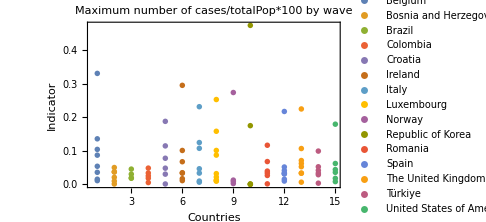
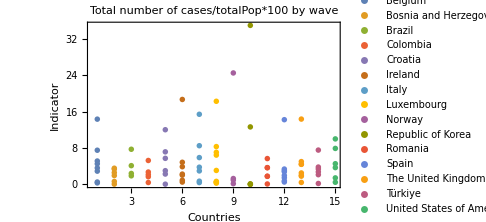
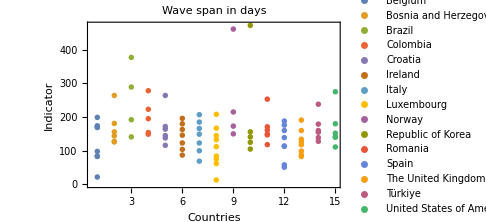
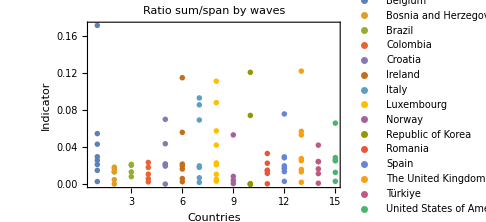

```mathematica
listPlot=ListPlot[#[[1]],PlotLabel->#[[2]],PlotRange->All,ImageSize->Medium,Frame->True,FrameLabel->{"Countries","Indicator"},PlotLegends->data2[[All,1,1]]]&/@{
{data2[[All,All,3]],"Maximum number of cases/totalPop*100 by wave"},
{data2[[All,All,4]],"Total number of cases/totalPop*100 by wave"},
{data2[[All,All,5]],"Wave span in days"},
{data2[[All,All,6]],"Ratio sum/span by waves"}}
```

### Plot2

For all the waves of each country  is made a BoxWhiskerChart of the “Total number of cases/totalPop*100”,  “Maximum number of cases/totalPop*100”, “Maximum number of cases/totalPop*100 normalized”

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

Maximum number of cases/totalPop*100 by wave

Total number of cases/totalPop*100 by wave

Wave span in days

Ratio sum/span by waves

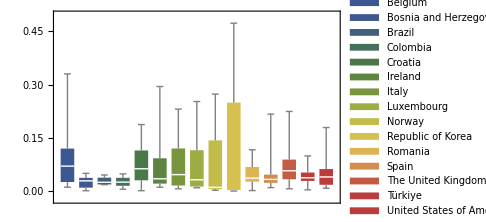
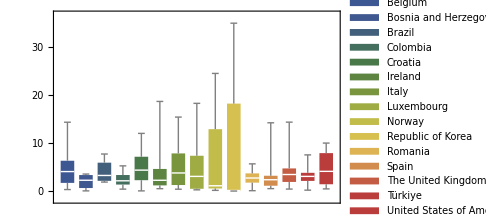
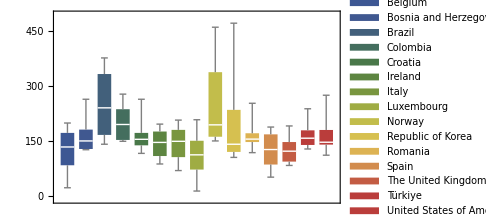
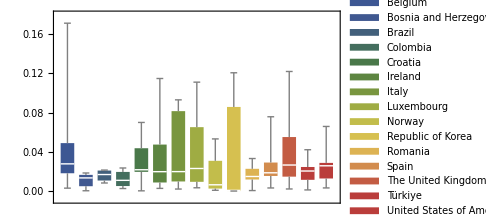

```mathematica
data3=GroupBy[data,First];
boxPlot=BoxWhiskerChart[#[[1]],ChartLabels->Echo[#[[2]]],ChartLegends->(data3[[2;;,1]]//Keys), ChartStyle->"DarkRainbow",ImageSize->Medium,FrameTicksStyle->Directive[Black,12]]&/@{
{data3[[2;;,All,3]],"Maximum number of cases/totalPop*100 by wave"},
{data3[[2;;,All,4]],"Total number of cases/totalPop*100 by wave"},
{data3[[2;;,All,5]],"Wave span in days"},
{data3[[2;;,All,6]],"Ratio sum/span by waves"}}
```

```mathematica
zz
```

### Plot 3

Merging the ListPlot and BoxWhiskerChart

```mathematica
listPlot2=ListPlot[#[[1]],PlotLabel->#[[2]],PlotRange->All,ImageSize->Medium,Frame->True,FrameLabel->{"Countries","Indicator"},PlotStyle->Black]&/@{{data2[[All,All,3]],"Maximum number of cases/totalPop*100 by wave"},
{data2[[All,All,4]],"Total number of cases/totalPop*100 by wave"},
{data2[[All,All,5]],"Wave span in days"},
{data2[[All,All,6]],"Ratio sum/span by waves"}};
(*This listPlot2 is the same as listPlot2 but without Legends*)

Show[boxPlot[[#]],listPlot2[[#]]]&/@{1,2,3,4}
```

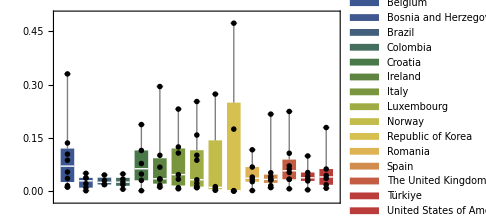
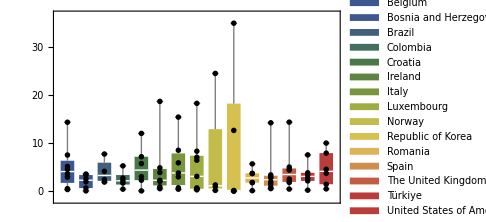
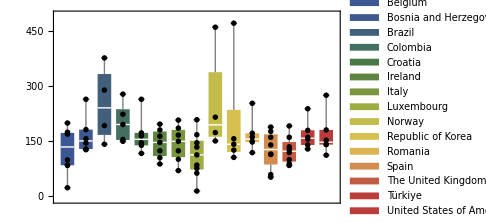
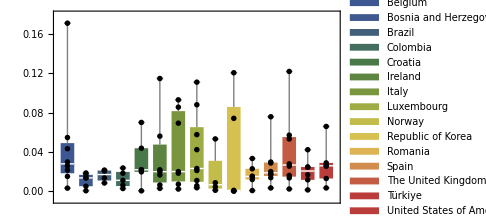

### Plot 4

Plotting the Total number of cases/totalPop*100”|”Maximum number of cases/totalPop*100”|”Maximum number of cases/totalPop*100 normalized”  values of for all the waves of all countries in a unique BoxWhiskerChart and repeating this plot as many countries there are

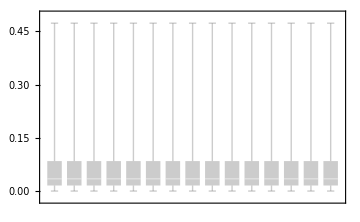
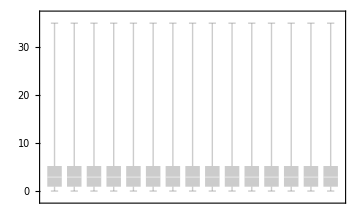
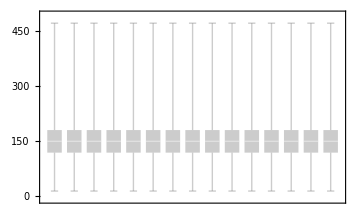
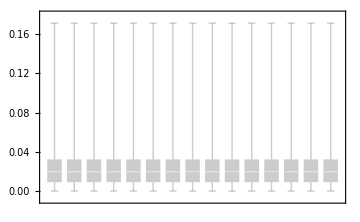

```mathematica
allBoxPlot=BoxWhiskerChart[Table[Flatten@GatherBy[data[[2;;]],First][[All,All,#[[1]]]],Length[data2[[All,1,1]]]],ImageSize->Medium,ChartStyle->Opacity[0.4,Gray],FrameTicksStyle->Directive[Black,12]]&/@{
{3,"Maximum number of cases/totalPop*100 by wave"},
{4,"Total number of cases/totalPop*100 by wave"},
{5,"Wave span in days"},
{6,"Ratio sum/span by waves"}}
```

### Plot 5

Plotting the Total number of cases/totalPop*100”|”Maximum number of cases/totalPop*100”|”Maximum number of cases/totalPop*100 normalized”  values of for all the waves of all countries in a unique BoxWhiskerChart and repeating this plot as many countries there are, and adding the points of the values belonging to each country

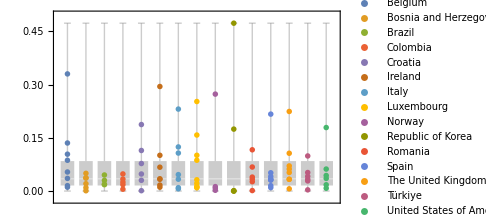
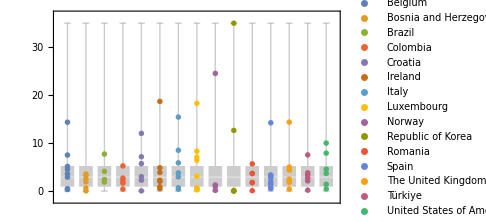
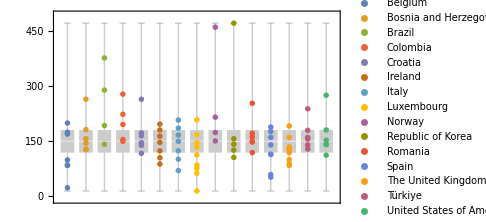
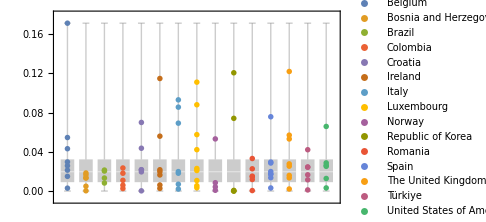

```mathematica
Show[allBoxPlot[[#]],listPlot[[#]]]&/@{1,2,3,4}
```

```mathematica
14/200.
```

0.07

### Summary of the estimations for each country

```mathematica
countries=data[[2;;,1]]//DeleteDuplicates
```

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

#### Maximum value

Getting some basic descriptions

```mathematica
descriptions={
#[[1]],
Min[#[[2]]],
Max[#[[2]]],
Mean[#[[2]]],
StandardDeviation[#[[2]]],
Variance[#[[2]]]
}&/@Thread[countries->GatherBy[data[[2;;]],First][[All,All,3]]];
```

Countries with the lowest Maximum value by wave

```mathematica
Select[descriptions,#[[2]]==Min[descriptions[[All,2]]]&][[All,{1,2}]]
```

{{Republic of Korea,0.000321497}}

Countries with the highest Maximum value by wave

```mathematica
Select[descriptions,#[[3]]==Max[descriptions[[All,3]]]&][[All,{1,3}]]
```

{{Republic of Korea,0.473144}}

Countries with the lowest mean of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[4]]==Min[descriptions[[All,4]]]&][[All,{1,4}]]
```

{{Bosnia and Herzegovina,0.0261266}}

Countries with the highest mean of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[4]]==Max[descriptions[[All,4]]]&][[All,{1,4}]]
```

{{Republic of Korea,0.130003}}

Countries with the lowest sd of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[5]]==Min[descriptions[[All,5]]]&][[All,{1,5}]]
```

{{Brazil,0.0126669}}

Countries with the highest sd of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[5]]==Max[descriptions[[All,5]]]&][[All,{1,5}]]
```

{{Republic of Korea,0.206104}}

Countries with the lowest variance of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[6]]==Min[descriptions[[All,6]]]&][[All,{1,6}]]
```

{{Brazil,0.000160449}}

Countries with the highest variance of  the maximum values of their set of waves

```mathematica
Select[descriptions,#[[6]]==Max[descriptions[[All,6]]]&][[All,{1,6}]]
```

{{Republic of Korea,0.042479}}

#### Total

Getting some basic descriptions

```mathematica
descriptionsT={
#[[1]],
Min[#[[2]]],
Max[#[[2]]],
Mean[#[[2]]],
StandardDeviation[#[[2]]],
Variance[#[[2]]]
}&/@Thread[countries->GatherBy[data[[2;;]],First][[All,All,4]]];
```

Countries with the lowest Total by wave

```mathematica
Select[descriptionsT,#[[2]]==Min[descriptionsT[[All,2]]]&][[All,{1,2}]]
```

{{Republic of Korea,0.0221261}}

Countries with the highest Total by wave

```mathematica
Select[descriptionsT,#[[3]]==Max[descriptionsT[[All,3]]]&][[All,{1,3}]]
```

{{Republic of Korea,35.0207}}

Countries with the lowest mean of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[4]]==Min[descriptionsT[[All,4]]]&][[All,{1,4}]]
```

{{Bosnia and Herzegovina,2.02968}}

Countries with the highest mean of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[4]]==Max[descriptionsT[[All,4]]]&][[All,{1,4}]]
```

{{Republic of Korea,9.57114}}

Countries with the lowest sd of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[5]]==Min[descriptionsT[[All,5]]]&][[All,{1,5}]]
```

{{Bosnia and Herzegovina,1.43133}}

Countries with the highest sd of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[5]]==Max[descriptionsT[[All,5]]]&][[All,{1,5}]]
```

{{Republic of Korea,15.2378}}

Countries with the lowest variance of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[6]]==Min[descriptionsT[[All,6]]]&][[All,{1,6}]]
```

{{Bosnia and Herzegovina,2.04872}}

Countries with the highest variance of  the totals of their set of waves

```mathematica
Select[descriptionsT,#[[6]]==Max[descriptionsT[[All,6]]]&][[All,{1,6}]]
```

{{Republic of Korea,232.192}}

#### Duration in days

Getting some basic descriptions

```mathematica
descriptionsD={
#[[1]],
Min[#[[2]]],
Max[#[[2]]],
Mean[#[[2]]],
StandardDeviation[#[[2]]],
Variance[#[[2]]]
}&/@Thread[countries->GatherBy[data[[2;;]],First][[All,All,5]]];
```

Countries with the lowest Duration in days by wave

```mathematica
Select[descriptionsD,#[[2]]==Min[descriptionsD[[All,2]]]&][[All,{1,2}]]
```

{{Luxembourg,13}}

Countries with the highest Duration in days by wave

```mathematica
Select[descriptionsD,#[[3]]==Max[descriptionsD[[All,3]]]&][[All,{1,3}]]
```

{{Republic of Korea,472}}

Countries with the lowest mean of  the Duration in days of their set of waves

```mathematica
Select[descriptionsD,#[[4]]==Min[descriptionsD[[All,4]]]&][[All,{1,4}]]
```

{{Luxembourg,111}}

Countries with the highest mean of  the Duration in days of their set of waves

```mathematica
N@Select[descriptionsD,#[[4]]==Max[descriptionsD[[All,4]]]&][[All,{1,4}]]
```

{{Brazil,249.75},{Norway,249.75}}

Countries with the lowest sd of  the Duration in days of their set of waves

```mathematica
N@Select[descriptionsD,#[[5]]==Min[descriptionsD[[All,5]]]&][[All,{1,5}]]
```

{{The United Kingdom,36.8799}}

Countries with the highest sd of  the Duration in days of their set of waves

```mathematica
N@Select[descriptionsD,#[[5]]==Max[descriptionsD[[All,5]]]&][[All,{1,5}]]
```

{{Republic of Korea,153.339}}

#### Ratio

Getting some basic descriptions

```mathematica
descriptionsR={
#[[1]],
Min[#[[2]]],
Max[#[[2]]],
Mean[#[[2]]],
StandardDeviation[#[[2]]],
Variance[#[[2]]]
}&/@Thread[countries->GatherBy[data[[2;;]],First][[All,All,6]]];
```

Countries with the lowest Ratio by wave

```mathematica
Select[descriptionsR,#[[2]]==Min[descriptionsR[[All,2]]]&][[All,{1,2}]]
```

{{Republic of Korea,0.000156923}}

Countries with the highest Ratio  by wave

```mathematica
Select[descriptionsR,#[[3]]==Max[descriptionsR[[All,3]]]&][[All,{1,3}]]
```

{{Belgium,0.171093}}

Countries with the lowest mean of  the ratio  of their set of waves

```mathematica
Select[descriptionsR,#[[4]]==Min[descriptionsR[[All,4]]]&][[All,{1,4}]]
```

{{Bosnia and Herzegovina,0.0112971}}

Countries with the highest mean of  the ratios  of their set of waves

```mathematica
Select[descriptionsR,#[[4]]==Max[descriptionsR[[All,4]]]&][[All,{1,4}]]
```

{{Belgium,0.0455433}}

Countries with the lowest sd of  the ratios of their set of waves

```mathematica
Select[descriptionsR,#[[5]]==Min[descriptionsR[[All,5]]]&][[All,{1,5}]]
```

{{Brazil,0.00622224}}

Countries with the highest sd of  the ratios of their set of waves

```mathematica
Select[descriptionsR,#[[5]]==Max[descriptionsR[[All,5]]]&][[All,{1,5}]]
```

{{Republic of Korea,0.0556096}}

{{Republic of Korea,0.0556096}}

### Summary of the estimations for all the countries at once

```mathematica
countries=data[[2;;,1]]//DeleteDuplicates
```

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

#### Maximum value

Getting some basic descriptions

```mathematica
descriptions={
Min[#],
Max[#],
Mean[#],
StandardDeviation[#]
}&@Flatten@GatherBy[data[[2;;]],First][[All,All,3]]
```

{0.000321497,0.473144,0.0663943,0.082382}

#### Total

Getting some basic descriptions

```mathematica
descriptions={
Min[#],
Max[#],
Mean[#],
StandardDeviation[#]
}&@Flatten@GatherBy[data[[2;;]],First][[All,All,4]]
```

{0.0221261,35.0207,4.51459,5.60897}

#### Duration in days

Getting some basic descriptions

```mathematica
descriptions=N@{
Min[#],
Max[#],
Mean[#],
StandardDeviation[#]
}&@Flatten@GatherBy[data[[2;;]],First][[All,All,5]]
```

{13.,472.,157.737,73.2588}

#### Ratio

Getting some basic descriptions

```mathematica
descriptions={
Min[#],
Max[#],
Mean[#],
StandardDeviation[#]
}&@Flatten@GatherBy[data[[2;;]],First][[All,All,6]]
```

{0.000156923,0.171093,0.0294827,0.0321815}

### ytf

```mathematica
GatherBy[data[[2;;]],First][[All,All,All]]
```

{{{Belgium,0,0.0111486,0.527596,170,0.00310351},{Belgium,1,0.104198,5.15112,199,0.025885},{Belgium,2,0.0359951,3.62356,169,0.0214412},{Belgium,3,0.135652,7.52842,174,0.0432668},{Belgium,4,0.330276,14.3718,84,0.171093},{Belgium,5,0.0870061,4.53648,83,0.0546563},{Belgium,6,0.0539906,2.91928,98,0.0297885},{Belgium,7,0.0155236,0.33246,22,0.0151118}},{{Bosnia and Herzegovina,0,0.0011789,0.0566137,126,0.000449315},{Bosnia and Herzegovina,1,0.0369286,3.56575,264,0.0135066},{Bosnia and Herzegovina,2,0.0374818,2.59585,156,0.0166401},{Bosnia and Herzegovina,3,0.0210718,1.95285,144,0.0135615},{Bosnia and Herzegovina,4,0.0501948,3.35687,181,0.0185463},{Bosnia and Herzegovina,5,0.00990378,0.650117,128,0.00507904}},{{Brazil,0,0.018229,2.41404,289,0.00835309},{Brazil,1,0.0304503,7.7416,377,0.0205348},{Brazil,2,0.0455621,4.13048,192,0.0215129},{Brazil,3,0.0195026,1.8903,141,0.0134064}},{{Colombia,0,0.0183685,1.694,278,0.00609354},{Colombia,1,0.025424,2.72477,149,0.018287},{Colombia,2,0.0484989,5.27128,223,0.023638},{Colombia,3,0.0339346,2.15699,195,0.0110615},{Colombia,4,0.00550584,0.418195,154,0.00271555}},{{Croatia,0,0.00133117,0.054485,145,0.000375758},{Croatia,1,0.0778543,5.74166,264,0.0217487},{Croatia,2,0.048322,3.02465,138,0.0219177},{Croatia,3,0.114587,7.17545,164,0.0437527},{Croatia,4,0.187626,12.0424,172,0.0700142},{Croatia,5,0.0305444,2.2848,116,0.0196965}},{{Ireland,0,0.0112088,0.514849,180,0.00286027},{Ireland,1,0.0171041,0.921178,146,0.00630944},{Ireland,2,0.0674906,3.89662,196,0.0198807},{Ireland,3,0.0335121,2.27121,104,0.0218385},{Ireland,4,0.294769,18.7071,163,0.114768},{Ireland,5,0.101009,4.87416,87,0.0560248},{Ireland,6,0.0348242,2.03547,123,0.0165485}},{{Italy,0,0.00661258,0.405639,185,0.00219265},{Italy,1,0.0465836,3.791,207,0.018314},{Italy,2,0.0336281,2.97226,149,0.019948},{Italy,3,0.00991803,0.71149,100,0.0071149},{Italy,4,0.231211,15.4426,166,0.0930278},{Italy,5,0.107337,5.90643,69,0.0856004},{Italy,6,0.124557,8.52152,123,0.0692806}},{{Luxembourg,0,0.0114512,0.504534,145,0.00347954},{Luxembourg,1,0.00950689,0.467637,84,0.0055671},{Luxembourg,2,0.0871602,7.06386,167,0.0422986},{Luxembourg,3,0.0320642,3.07664,133,0.0231326},{Luxembourg,4,0.0133203,0.674317,62,0.0108761},{Luxembourg,5,0.252525,18.307,208,0.0880146},{Luxembourg,6,0.1581,8.32827,75,0.111044},{Luxembourg,7,0.101047,6.45219,112,0.0576088},{Luxembourg,8,0.0219885,0.27403,13,0.0210793}},{{Norway,0,0.00248778,0.162723,173,0.000940598},{Norway,1,0.00852052,0.946853,215,0.00440397},{Norway,2,0.0127933,1.29546,150,0.00863637},{Norway,3,0.273392,24.5457,461,0.0532445}},{{Republic of Korea,0,0.000352074,0.0221261,141,0.000156923},{Republic of Korea,1,0.000321497,0.0221848,125,0.000177478},{Republic of Korea,2,0.00140429,0.128329,156,0.000822621},{Republic of Korea,3,0.473144,35.0207,472,0.0741964},{Republic of Korea,4,0.174792,12.6624,105,0.120594}},{{Romania,0,0.00168982,0.0954426,147,0.000649269},{Romania,1,0.0396329,3.70319,253,0.0146371},{Romania,2,0.0266035,1.77462,149,0.0119102},{Romania,3,0.0679816,3.67165,161,0.0228053},{Romania,4,0.116524,5.68983,171,0.0332739},{Romania,5,0.0337081,1.80743,118,0.0153172}},{{Spain,0,0.00992989,0.526468,160,0.00329043},{Spain,1,0.0344547,3.04108,176,0.0172789},{Spain,2,0.0517888,3.38209,114,0.0296674},{Spain,3,0.0155218,0.797434,58,0.0137489},{Spain,4,0.041459,2.77989,139,0.0199992},{Spain,5,0.217017,14.2524,188,0.0758105},{Spain,6,0.0311552,1.46332,51,0.0286925},{Spain,7,0.0318019,1.97462,113,0.0174746}},{{The United Kingdom,0,0.00661976,0.432786,191,0.0022659},{The United Kingdom,1,0.0334129,1.81581,134,0.0135508},{The United Kingdom,2,0.0710818,4.45072,160,0.027817},{The United Kingdom,3,0.0526185,2.52363,99,0.0254912},{The United Kingdom,4,0.0622485,4.41654,83,0.0532113},{The United Kingdom,5,0.224487,14.3864,118,0.121919},{The United Kingdom,6,0.106747,5.02263,88,0.0570753},{The United Kingdom,7,0.0334592,2.02748,126,0.0160911}},{{Türkiye,0,0.00367849,0.206477,160,0.00129048},{Türkiye,1,0.028792,2.75873,238,0.0115913},{Türkiye,2,0.0524771,3.39335,139,0.0244126},{Türkiye,3,0.0335337,3.82151,155,0.0246549},{Türkiye,4,0.099165,7.56002,179,0.0422348},{Türkiye,5,0.0417738,2.13845,128,0.0167066}},{{United States of America,0,0.00827781,0.469194,141,0.00332761},{United States of America,1,0.0179699,1.43674,111,0.0129436},{United States of America,2,0.0622513,7.9263,275,0.0288229},{United States of America,3,0.0440912,3.69775,140,0.0264125},{United States of America,4,0.179187,10.0222,152,0.0659355},{United States of America,5,0.0358905,4.55907,180,0.0253282}}}

```mathematica
SortBy[#,Last]&@Flatten[#,1]&@GatherBy[data[[2;;]],First][[All,All,All]]
```

{{Republic of Korea,0,0.000352074,0.0221261,141,0.000156923},{Republic of Korea,1,0.000321497,0.0221848,125,0.000177478},{Croatia,0,0.00133117,0.054485,145,0.000375758},{Bosnia and Herzegovina,0,0.0011789,0.0566137,126,0.000449315},{Romania,0,0.00168982,0.0954426,147,0.000649269},{Republic of Korea,2,0.00140429,0.128329,156,0.000822621},{Norway,0,0.00248778,0.162723,173,0.000940598},{Türkiye,0,0.00367849,0.206477,160,0.00129048},{Italy,0,0.00661258,0.405639,185,0.00219265},{The United Kingdom,0,0.00661976,0.432786,191,0.0022659},{Colombia,4,0.00550584,0.418195,154,0.00271555},{Ireland,0,0.0112088,0.514849,180,0.00286027},{Belgium,0,0.0111486,0.527596,170,0.00310351},{Spain,0,0.00992989,0.526468,160,0.00329043},{United States of America,0,0.00827781,0.469194,141,0.00332761},{Luxembourg,0,0.0114512,0.504534,145,0.00347954},{Norway,1,0.00852052,0.946853,215,0.00440397},{Bosnia and Herzegovina,5,0.00990378,0.650117,128,0.00507904},{Luxembourg,1,0.00950689,0.467637,84,0.0055671},{Colombia,0,0.0183685,1.694,278,0.00609354},{Ireland,1,0.0171041,0.921178,146,0.00630944},{Italy,3,0.00991803,0.71149,100,0.0071149},{Brazil,0,0.018229,2.41404,289,0.00835309},{Norway,2,0.0127933,1.29546,150,0.00863637},{Luxembourg,4,0.0133203,0.674317,62,0.0108761},{Colombia,3,0.0339346,2.15699,195,0.0110615},{Türkiye,1,0.028792,2.75873,238,0.0115913},{Romania,2,0.0266035,1.77462,149,0.0119102},{United States of America,1,0.0179699,1.43674,111,0.0129436},{Brazil,3,0.0195026,1.8903,141,0.0134064},{Bosnia and Herzegovina,1,0.0369286,3.56575,264,0.0135066},{The United Kingdom,1,0.0334129,1.81581,134,0.0135508},{Bosnia and Herzegovina,3,0.0210718,1.95285,144,0.0135615},{Spain,3,0.0155218,0.797434,58,0.0137489},{Romania,1,0.0396329,3.70319,253,0.0146371},{Belgium,7,0.0155236,0.33246,22,0.0151118},{Romania,5,0.0337081,1.80743,118,0.0153172},{The United Kingdom,7,0.0334592,2.02748,126,0.0160911},{Ireland,6,0.0348242,2.03547,123,0.0165485},{Bosnia and Herzegovina,2,0.0374818,2.59585,156,0.0166401},{Türkiye,5,0.0417738,2.13845,128,0.0167066},{Spain,1,0.0344547,3.04108,176,0.0172789},{Spain,7,0.0318019,1.97462,113,0.0174746},{Colombia,1,0.025424,2.72477,149,0.018287},{Italy,1,0.0465836,3.791,207,0.018314},{Bosnia and Herzegovina,4,0.0501948,3.35687,181,0.0185463},{Croatia,5,0.0305444,2.2848,116,0.0196965},{Ireland,2,0.0674906,3.89662,196,0.0198807},{Italy,2,0.0336281,2.97226,149,0.019948},{Spain,4,0.041459,2.77989,139,0.0199992},{Brazil,1,0.0304503,7.7416,377,0.0205348},{Luxembourg,8,0.0219885,0.27403,13,0.0210793},{Belgium,2,0.0359951,3.62356,169,0.0214412},{Brazil,2,0.0455621,4.13048,192,0.0215129},{Croatia,1,0.0778543,5.74166,264,0.0217487},{Ireland,3,0.0335121,2.27121,104,0.0218385},{Croatia,2,0.048322,3.02465,138,0.0219177},{Romania,3,0.0679816,3.67165,161,0.0228053},{Luxembourg,3,0.0320642,3.07664,133,0.0231326},{Colombia,2,0.0484989,5.27128,223,0.023638},{Türkiye,2,0.0524771,3.39335,139,0.0244126},{Türkiye,3,0.0335337,3.82151,155,0.0246549},{United States of America,5,0.0358905,4.55907,180,0.0253282},{The United Kingdom,3,0.0526185,2.52363,99,0.0254912},{Belgium,1,0.104198,5.15112,199,0.025885},{United States of America,3,0.0440912,3.69775,140,0.0264125},{The United Kingdom,2,0.0710818,4.45072,160,0.027817},{Spain,6,0.0311552,1.46332,51,0.0286925},{United States of America,2,0.0622513,7.9263,275,0.0288229},{Spain,2,0.0517888,3.38209,114,0.0296674},{Belgium,6,0.0539906,2.91928,98,0.0297885},{Romania,4,0.116524,5.68983,171,0.0332739},{Türkiye,4,0.099165,7.56002,179,0.0422348},{Luxembourg,2,0.0871602,7.06386,167,0.0422986},{Belgium,3,0.135652,7.52842,174,0.0432668},{Croatia,3,0.114587,7.17545,164,0.0437527},{The United Kingdom,4,0.0622485,4.41654,83,0.0532113},{Norway,3,0.273392,24.5457,461,0.0532445},{Belgium,5,0.0870061,4.53648,83,0.0546563},{Ireland,5,0.101009,4.87416,87,0.0560248},{The United Kingdom,6,0.106747,5.02263,88,0.0570753},{Luxembourg,7,0.101047,6.45219,112,0.0576088},{United States of America,4,0.179187,10.0222,152,0.0659355},{Italy,6,0.124557,8.52152,123,0.0692806},{Croatia,4,0.187626,12.0424,172,0.0700142},{Republic of Korea,3,0.473144,35.0207,472,0.0741964},{Spain,5,0.217017,14.2524,188,0.0758105},{Italy,5,0.107337,5.90643,69,0.0856004},{Luxembourg,5,0.252525,18.307,208,0.0880146},{Italy,4,0.231211,15.4426,166,0.0930278},{Luxembourg,6,0.1581,8.32827,75,0.111044},{Ireland,4,0.294769,18.7071,163,0.114768},{Republic of Korea,4,0.174792,12.6624,105,0.120594},{The United Kingdom,5,0.224487,14.3864,118,0.121919},{Belgium,4,0.330276,14.3718,84,0.171093}}